## Define Potential & Solve for Cosmological Parameters

nff = -1.6

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-0.872529,0.605467}

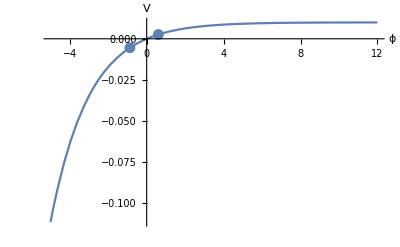

vacuumArray = {}

ϕ0 = 0.605467

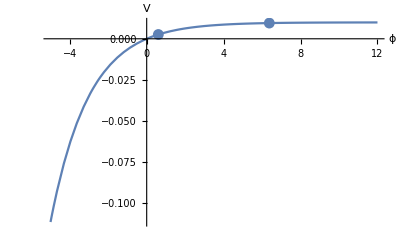

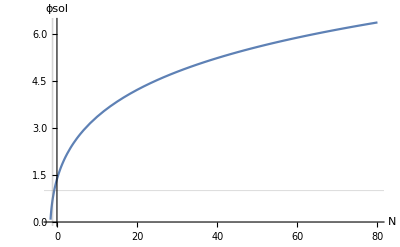

At n = 0, ϵ1 = 0.101007

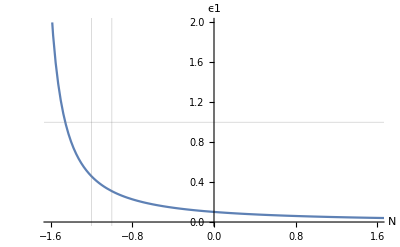

InterpolatingFunction::dmval: Input value {-2.3017} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87695} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.70219} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

roots = {n→-1.45583}

At n1 = -1.45583, ϵ1 = 1.

ϕi2 = 6.34442

ϕpi2 = 0.0217909

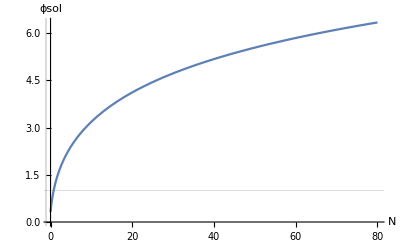

ϕsol2[60] = 5.85001

At n = 0, ϵ1 = 1.00011

ns[60] = 0.969541

r[60] = 0.00636835

```mathematica
(* Define an inflationary potential *)
left = False;
(*v[x_]:=(0.1)*(1+Log[x]); *)
v[x_]:=(0.01)*(1-Exp[-0.5*x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
(*While[nf<-eps,
Print["nf = ",nf];
ϕsol2=Catch[findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left]];
Print["ϕsol2 = ",ϕsol2];
If[ϕsol2==="n1 = 1/0",Print["Again!"];nf=nf+0.2,Print["BREAK!"];Break[]];
];*)
ϕsol2=findϕsolnfLoop[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left,0.2];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.847467}

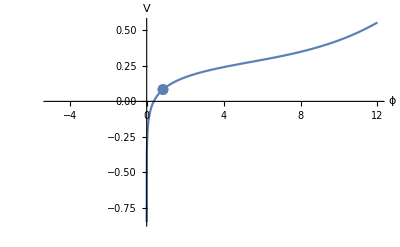

vacuumArray = {}

ϕ0 = 0.847467

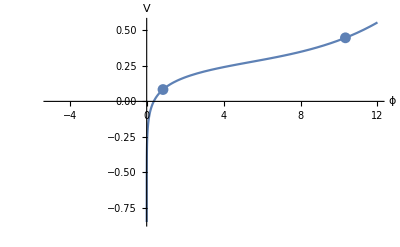

NDSolve::ndsz: At n == -1.04614, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-2.79831} lies outside the range of data in the interpolating function. Extrapolation will be used.

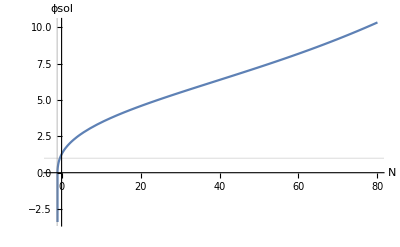

At n = 0, ϵ1 = 0.14115

InterpolatingFunction::dmval: Input value {-2.79831} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

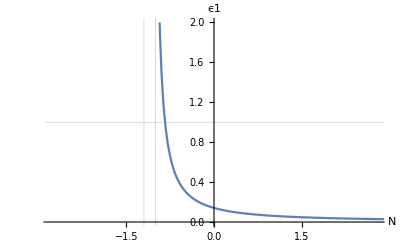

At n1 = -0.838599, ϵ1 = 1.

ϕi2 = 10.2338

ϕpi2 = 0.119478

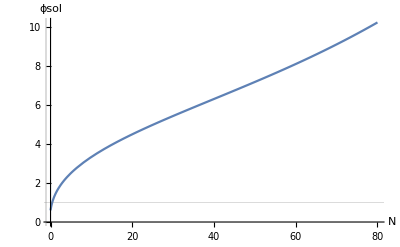

ϕsol2[60] = 8.10142

At n = 0, ϵ1 = 1.

ns[60] = 1.00895

r[60] = 0.0732722

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.1)*(1+Log[x]+0.0001*x^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

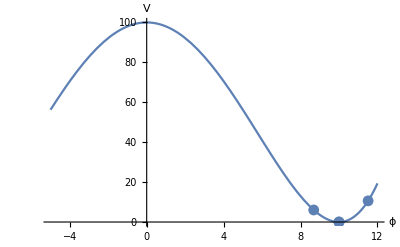

vacuumArray = {10.,10.}

ϕ0 = 11.5137

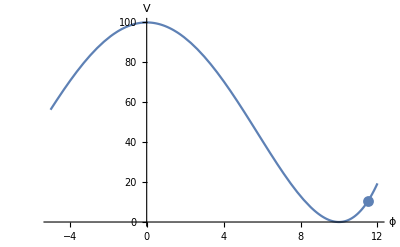

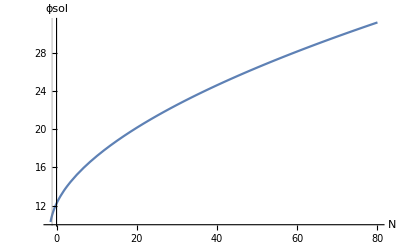

At n = 0, ϵ1 = 0.393544

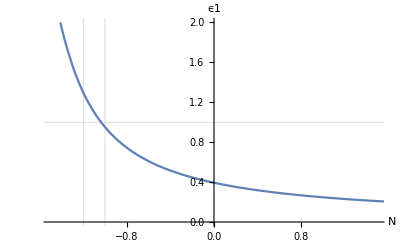

At n1 = -1.03609, ϵ1 = 1.

ϕi2 = 31.0248

ϕpi2 = 0.143616

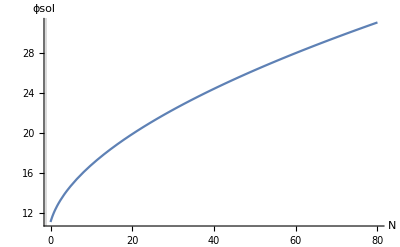

ϕsol2[60] = 27.9666

At n = 0, ϵ1 = 1.

ns[60] = 0.958194

r[60] = 0.214077

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.01)*((x^2-(10)^2)^2 );(*(Tanh[x]+0.00001*x^4);*)
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -1.5; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-0.872529,0.605467}

-Graphics-

vacuumArray = {}

ϕ0 = 0.605467

-Graphics-

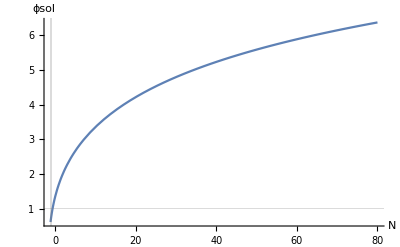

At n = 0, ϵ1 = 0.101007

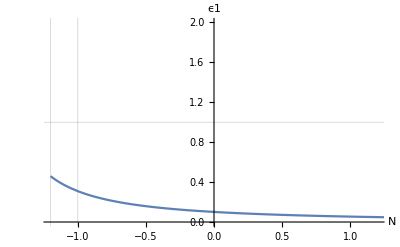

InterpolatingFunction::dmval: Input value {-2.3017} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87695} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.20485} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

roots = 1/0 Error

THROW!

Throw::nocatch: Uncaught Throw["n1 = 1/0"] returned to top level.

Hold[Throw[n1 = 1/0]]

ReplaceAll::reps: {"n1 = 1/0"} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

At n = 0, ϵ1 = (3 (ϕ'[0]/.n1 = 1/0)^2)/((0.02 (1-ⅇ^(-0.5 ϕ[0])))/((0.01 (1-ⅇ^(-0.5 ϕ[0])))/(3-1/2 (ϕ'[0]/.n1 = 1/0)^2)/.n1 = 1/0)+(ϕ'[0]/.n1 = 1/0)^2)/.n1 = 1/0

General::ivar: 60 is not a valid variable.

ns[60] = 1+(∂_60 ((3 (ϕ'[60]/.n1 = 1/0)^2)/((0.02 (1-ⅇ^(-0.5 ϕ[60])))/((0.01 (1-ⅇ^(-0.5 ϕ[60])))/(3-1/2 (ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)+(ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0))/((3 (ϕ'[60]/.n1 = 1/0)^2)/((0.02 (1-ⅇ^(-0.5 ϕ[60])))/((0.01 (1-ⅇ^(-0.5 ϕ[60])))/(3-1/2 (ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)+(ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)-2 ((3 (ϕ'[60]/.n1 = 1/0)^2)/((0.02 (1-ⅇ^(-0.5 ϕ[60])))/((0.01 (1-ⅇ^(-0.5 ϕ[60])))/(3-1/2 (ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)+(ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)

r[60] = 16 ((3 (ϕ'[60]/.n1 = 1/0)^2)/((0.02 (1-ⅇ^(-0.5 ϕ[60])))/((0.01 (1-ⅇ^(-0.5 ϕ[60])))/(3-1/2 (ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)+(ϕ'[60]/.n1 = 1/0)^2)/.n1 = 1/0)

```mathematica
(* Define an inflationary potential *)
left = False;
(* v[x_]:=(0.01)*((x^2-(10)^2)^2 +0.00001*x^6);*)
(*v[x_]:=Tanh[x/1.1];(*+0.00001*x^4;*)
v=vacuumShift[v];*)
v[x_]:=(0.01)*(1-Exp[-0.5*x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -1.2; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```